# CNN Codes

## Import Data

NCEP

#### GPH

```mathematica
GPH=Block[{file,minlat=22.5,maxlat=55.,minlon=212.5,maxlon=247.5,height=850.,
		   lat,lon,level,indexlat,indexlon,indexlevel},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH"];
	file=FileNames["*.nc"];
	{lat,lon,level}=Import[file[[1]],{"Datasets",{"lat","lon","level"}}];
	indexlat=Sort[Map[Position[lat,#][[1,1]]&,{minlat,maxlat}]];
	indexlon=Sort[Map[Position[lon,#][[1,1]]&,{minlon,maxlon}]];
	indexlevel=Position[level,height][[1,1]];
	Map[Import[#,{"Datasets","hgt"}][[;;,indexlevel,indexlat[[1]];;indexlat[[2]],indexlon[[1]];;indexlon[[2]]]]&,
			file]];
```

```mathematica
Export["/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH/WestCoast/GPH.mx",GPH];
```

```mathematica
GPH=Import["/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH/WestCoast/GPH.mx"];
```

```mathematica
Dimensions[GPH]
```

{70}

#### Precipitation

```mathematica
testpoint[polygon_,pt_]:=Round[Total[Mod[(#1-RotateRight[#1]&)[(ArcTan@@(pt-#1)&)/@polygon],2 π,-π]]/(2 π)]≠0
```

```mathematica
Precip=Block[{file,scope,net,indexes},
	scope={{51,235},{51,241},{39,241},{34,246},{31,246},{31,242},{38,235}};
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/Precipitation"];
	file=FileNames["*.nc"];
	{lat,lon}=Import[file[[1]],{"Datasets",{"lat","lon"}}];
	net=Table[Table[{lat[[i]],lon[[j]]},{j,1,Length[lon]}],{i,1,Length[lat]}];
	net=Select[Flatten[net,1],And[#[[1]]>20,#[[2]]>180,#[[1]]<55,#[[2]]<260]&];
	indexes=Map[{Position[lat,#[[1]]][[1,1]],Position[lon,#[[2]]][[1,1]]}&,Select[net,testpoint[scope,#]&]];
	Table[Block[{data=Import[file[[i]],{"Datasets","prate"}]},
		Map[data[[;;,#[[1]],#[[2]]]]&,indexes]],
			{i,Length[file]}]];
```

```mathematica
Export["/Users/lambda/Documents/Data/NCEP_Reanalysis/Precipitation/WestCoast/Precip.mx",Precip];
```

```mathematica
Precip=Import["/Users/lambda/Documents/Data/NCEP_Reanalysis/Precipitation/WestCoast/Precip.mx"];
```

```mathematica
Dimensions[Precip]
```

{70,36}

ECMWF

#### GPH

```mathematica
GPH=Block[{file,minlat=22.5,maxlat=55.,minlon=212.5,maxlon=247.5,height=850.,
		   lat,lon,level,indexlat,indexlon,indexlevel},
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH"];
	file=FileNames["*.nc"];
	{lat,lon,level}=Import[file[[1]],{"Datasets",{"lat","lon","level"}}];
	indexlat=Sort[Map[Position[lat,#][[1,1]]&,{minlat,maxlat}]];
	indexlon=Sort[Map[Position[lon,#][[1,1]]&,{minlon,maxlon}]];
	indexlevel=Position[level,height][[1,1]];
	Map[Import[#,{"Datasets","hgt"}][[;;,indexlevel,indexlat[[1]];;indexlat[[2]],indexlon[[1]];;indexlon[[2]]]]&,
			file]];
```

```mathematica
Export["/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH/WestCoast/GPH.mx",GPH];
```

```mathematica
GPH=Import["/Users/lambda/Documents/Data/NCEP_Reanalysis/GPH/WestCoast/GPH.mx"];
```

```mathematica
Dimensions[GPH]
```

{70}

#### Precipitation

```mathematica
Precip=Block[{file,scope,net,indexes},
	scope={{51,235},{51,241},{39,241},{34,246},{31,246},{31,242},{38,235}};
	SetDirectory["/Users/lambda/Documents/Data/NCEP_Reanalysis/Precipitation"];
	file=FileNames["*.nc"];
	{lat,lon}=Import[file[[1]],{"Datasets",{"lat","lon"}}];
	net=Table[Table[{lat[[i]],lon[[j]]},{j,1,Length[lon]}],{i,1,Length[lat]}];
	net=Select[Flatten[net,1],And[#[[1]]>20,#[[2]]>180,#[[1]]<55,#[[2]]<260]&];
	indexes=Map[{Position[lat,#[[1]]][[1,1]],Position[lon,#[[2]]][[1,1]]}&,Select[net,testpoint[scope,#]&]];
	Table[Block[{data=Import[file[[i]],{"Datasets","prate"}]},
		Map[data[[;;,#[[1]],#[[2]]]]&,indexes]],
			{i,Length[file]}]];
```

```mathematica
Dimensions[Precip]
```

{70,36}

CPC Gauge

```mathematica
Precip=Block[{file,scope,net,indexes},
	SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
	file=FileNames["*.nc"][[1;;-2]];
	{lat,lon}=Import[file[[1]],{"Datasets",{"lat","lon"}}];
	scope={{50,235},{50,240},{38,240},{34,246},{32,246},{32,242},{38,235}};
	net=Table[Table[{lat[[i]],lon[[j]]},{j,1,Length[lon]}],{i,1,Length[lat]}];
	net=Select[Flatten[net,1],And[#[[1]]>20,#[[2]]>180,#[[1]]<55,#[[2]]<260]&];
	indexes=Map[{Position[lat,#[[1]]][[1,1]],Position[lon,#[[2]]][[1,1]]}&,Select[net,testpoint[scope,#]&]];
	Table[Block[{data=Import[file[[i]],{"Datasets","precip"}]},
		Map[data[[;;,#[[1]],#[[2]]]]&,indexes]],
			{i,Length[file]}]];
```

```mathematica
Export["/Users/lambda/Documents/Data/CPC_Precipitation/Precip.mx",Precip];
```

```mathematica
Precip=Import["/Users/lambda/Documents/Data/CPC_Precipitation/Precip.mx"];
```

```mathematica
Dimensions[Precip]
```

{59,1488}

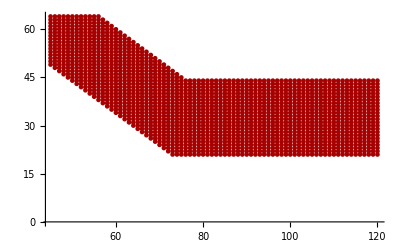

```mathematica
ListPlot[indexes]
```

```mathematica
SetDirectory["/Users/lambda/Downloads"];
lat=Import["data.nc",{"Datasets","Y"}];
lon=Import["data.nc",{"Datasets","X"}];
time=Import["data.nc",{"Datasets","T"}];
```

```mathematica
p=Import["data.nc",{"Datasets","rain"}];
```

Import::fmterr: Cannot import data as NetCDF format.

```mathematica
NSC[simu_,obser_]:=1-Total[(simu-obser)^2]/Total[(obser-Mean[obser])^2]
```

## CNN

Whole Year & 6h

```mathematica
gph=Block[{data=Map[{#}&,Flatten[GPH,1]],mean,std},
	std=Sqrt[Variance[data]];
	mean=Mean[data];
	Map[(#-mean)/std&,data]];
precip=Block[{data=Flatten[Table[Transpose[Precip[[i]]],{i,Length[Precip]}],1],mean,std},
	mean=Mean[data];
	std=Sqrt[Variance[data]];
	Map[(#-mean)/std&,data]];
l=Min[Length[gph],Length[precip]];
{gph,precip}=Transpose[RandomSample[Transpose[{gph[[1;;l]],precip[[1;;l]]}]]];
Dimensions[gph]
Dimensions[precip]
```

{101512,1,14,15}

{101512,36}

```mathematica
Export["6h_GPH.mx",gph]
Export["6h_P.mx",precip]
```

6h_GPH.mx

6h_P.mx

```mathematica
ann=NetInitialize[NetChain[{
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 BatchNormalizationLayer[],
						 
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 BatchNormalizationLayer[],
						 PoolingLayer[2, 1],
						
						 FlattenLayer[], 
					 
						
						
						 180,
						 ElementwiseLayer[Ramp],
						 BatchNormalizationLayer[],
						 144,
						 ElementwiseLayer[Ramp],
						 BatchNormalizationLayer[],
						 36
						 },  
					"Input" -> {1,14,15},
					"Output" -> {36}]]
```

NetChain[]

```mathematica
ann=Block[{ptraining=Floor[Length[precip]*0.7]},
	NetTrain[ann,
	gph[[1;;ptraining]]->precip[[1;;ptraining]],
    ValidationSet->Table[gph[[i]]->precip[[i]],{i,ptraining,Min[Length[gph],Length[precip]]}],
	Method->{"ADAM","LearningRate"->0.01,"L2Regularization"->0.05},
	BatchSize->12700,
	MaxTrainingRounds -> 2000]]
```

NetChain[]

```mathematica
ann=Import["/Users/lambda/Documents/S2S/Results/ann_6h_v4.mx"]
```

NetChain[]

```mathematica
Export["/Users/lambda/Documents/S2S/Results/ann_6h.mx",ann]
```

/Users/lambda/Documents/S2S/Results/ann_6h.mx

```mathematica
simu=Block[{data=Flatten[Table[Transpose[Precip[[i]]],{i,Length[Precip]}],1],mean,std},
	mean=Mean[data];
	std=Sqrt[Variance[data]];
	Map[#*std+mean&,ann@gph]];
ptraining=Floor[Length[precip]*0.7];
result=Table[Correlation[simu[[ptraining;;Length[precip],i]],precip[[ptraining;,i]]],{i,36}]
Mean[result]
MinMax[result]
result=Table[Correlation[simu[[1;;ptraining,i]],precip[[1;;ptraining,i]]],{i,36}]
Mean[result]
MinMax[result]
```

Part::pkspec1: The expression Null cannot be used as a part specification.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Part::pkspec1: The expression Null cannot be used as a part specification.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Part::pkspec1: The expression Null cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

General::stop: Further output of Correlation::vctmat will be suppressed during this calculation.

$Aborted[]

Part::pkspec1: The expression Null cannot be used as a part specification.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Part::pkspec1: The expression Null cannot be used as a part specification.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

Part::pkspec1: The expression Null cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Correlation::vctmat: The arguments to Correlation are not a pair of vectors or a pair of matrices of equal length.

General::stop: Further output of Correlation::vctmat will be suppressed during this calculation.

#### Linear

```mathematica
linear = Predict[trainingset, Method -> "LinearRegression"]
```

Whole Year & 1day

```mathematica
ReScale[data_,times_]:=Table[Mean[data[[i;;i+times-1]]],{i,1,Length[data],times}];
```

```mathematica
gph=Block[{data=ReScale[Map[{#}&,Flatten[GPH,1]],4],mean,std},
	std=Sqrt[Variance[data]];
	mean=Mean[data];
	Map[(#-mean)/std&,data]];
precip=Block[{data=ReScale[Flatten[Table[Transpose[Precip[[i]]],{i,Length[Precip]}],1],4],mean,std},
	mean=Mean[data];
	std=Sqrt[Variance[data]];
	Map[(#-mean)/std&,data]];
l=Min[Length[gph],Length[precip]];
{gph,precip}=Transpose[RandomSample[Transpose[{gph[[1;;l]],precip[[1;;l]]}]]];
Dimensions[gph]
Dimensions[precip]
```

{25378,1,14,15}

{25378,36}

```mathematica
CNN=NetInitialize[NetChain[{
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 PoolingLayer[2, 1],
						 FlattenLayer[], 
						 DropoutLayer[0.2],
						 BatchNormalizationLayer[],
						 120,
						 ElementwiseLayer[Ramp],
						 DropoutLayer[0.2],
						 BatchNormalizationLayer[],
						 100,
						 ElementwiseLayer[Ramp],
						 36,
						 BatchNormalizationLayer[]
						 },  
					"Input" -> {1,14,15},
					"Output" -> {36}]]
```

NetChain[]

```mathematica
ann=Block[{ptraining=Floor[Length[precip]*0.7]},
	NetTrain[ann,
	gph[[1;;ptraining]]->precip[[1;;ptraining]],
	ValidationSet->Table[gph[[i]]->precip[[i]],{i,ptraining,Min[Length[gph],Length[precip]]}],
	Method->{"ADAM"(*"LearningRate"->0.00001*),"L2Regularization"->0.08},
	BatchSize->2500,
	MaxTrainingRounds -> 2000]]
```

NetChain[]

```mathematica
Export["ann_1day_2.mx",ann]
```

ann_1day_2.mx

```mathematica
ann=Import["ann.mx"];
```

```mathematica
NSC[simu_,obser_]:=1-Total[(simu-obser)^2]/Total[(obser-Mean[obser])^2]
```

```mathematica
simu=Block[{data=Flatten[Table[Transpose[Precip[[i]]],{i,Length[Precip]}],1],mean,std},
	mean=Mean[data];
	std=Sqrt[Variance[data]];
	Map[#*std+mean&,ann@gph]];
result=Table[Correlation[simu[[1;;Length[precip],i]],precip[[;;,i]]],{i,36}]
Mean[result]
MinMax[result]
```

{0.77672,0.76215,0.688306,0.83705,0.844799,0.825916,0.823368,0.796873,0.721697,0.814892,0.759764,0.612402,0.843503,0.813347,0.617202,0.853096,0.861509,0.758986,0.83639,0.865715,0.842619,0.788954,0.856266,0.853727,0.800887,0.798099,0.819058,0.809012,0.731124,0.770541,0.760332,0.71061,0.669496,0.687731,0.603727,0.547094}

0.771193

{0.547094,0.865715}

## CNN

Boreal Winter

```mathematica
winter=Flatten[Table[{Range[1+year*365*4,90*4+year*365*4],
					  Range[270*4+year*365*4,365*4+year*365*4]},{year,0,68}]];
```

```mathematica
gph=Block[{data=Map[{#}&,Flatten[GPH,1]][[winter]],mean,std},
	std=Sqrt[Variance[data]];
	mean=Mean[data];
	Map[(#-mean)/std&,data]];
precip=Block[{data=Flatten[Table[Transpose[Precip[[i]]],{i,Length[Precip]}],1][[winter]],mean,std},
	mean=Mean[data];
	std=Sqrt[Variance[data]];
	Map[(#-mean)/std&,data]];
{gph,precip}=Transpose[RandomSample[Transpose[{gph,precip}]]];
Dimensions[gph]
Dimensions[precip]
```

{51129,1,14,15}

{51129,36}

```mathematica
CNN=NetInitialize[NetChain[{
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						 
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 ConvolutionLayer[1, 3],
						 ElementwiseLayer[Ramp],
						  
						 PoolingLayer[2, 1],
						  DropoutLayer[0.2],
						 FlattenLayer[], 
						 BatchNormalizationLayer[], 
						 DropoutLayer[0.2],
						 200,
						 ElementwiseLayer[Ramp],
						
						 BatchNormalizationLayer[],  
						  DropoutLayer[0.2],
						 200,
						 ElementwiseLayer[Ramp],
						 36
						 },  
					"Input" -> {1,14,15},
					"Output" -> {36}]]
```

NetChain[]

```mathematica
ann=Block[{ptraining=Floor[Length[precip]*0.7]},
	NetTrain[ann,
	gph[[1;;ptraining]]->precip[[1;;ptraining]],
	ValidationSet->Table[gph[[i]]->precip[[i]],{i,ptraining,Min[Length[gph],Length[precip]]}],
	Method->{"ADAM","L2Regularization"->0.1},
	BatchSize->400,
	MaxTrainingRounds -> 2000]]
```

NetChain[]

```mathematica
simu=Block[{data=Flatten[Table[Transpose[Precip[[i]]],{i,Length[Precip]}],1][[winter]],mean,std},
	mean=Mean[data];
	std=Sqrt[Variance[data]];
	Map[#*std+mean&,ann@gph]];
result=Table[Correlation[simu[[1;;Length[winter],i]],precip[[;;,i]]],{i,36}]
Mean[result]
MinMax[result]
```

{0.779286,0.789386,0.756551,0.820571,0.841948,0.828908,0.790771,0.804149,0.765656,0.798349,0.806007,0.746721,0.831404,0.842632,0.757654,0.847644,0.87798,0.830045,0.859235,0.896911,0.882465,0.834963,0.888927,0.905746,0.894863,0.865312,0.902417,0.907567,0.865171,0.869544,0.899438,0.838122,0.745948,0.833341,0.863,0.789996}

0.834962

{0.745948,0.907567}

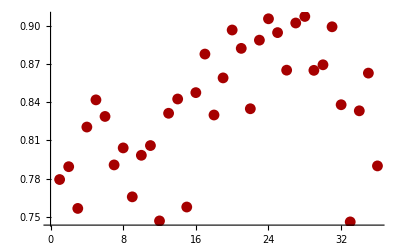

```mathematica
ListPlot[result]
```